```mathematica
Series[u^n/(Kn+u^n),{Kn,0,2},Assumptions->n>1&&u>0]
```

1-u^-n Kn+u^(-2 n) Kn^2+O[Kn]^3

```mathematica
Solve[u^n/(K^n+u^n)==u,u,NonNegativeReals,Assumptions->n>1&&K>0]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[u^n/(K^n+u^n)==u,u,,Assumptions→n>1&&K>0]

```mathematica
AsymptoticSolve[u^n/(K^n+u^n)==u,{u},{K,0,1},Assumptions->n==2]
```

AsymptoticSolve[u^n/(K^n+u^n)==u,{u},{K,0,1},Assumptions→n==2]

```mathematica
Series[x^n/(K^n+x^n),{x,K,2},Assumptions->n>0]
```

1/2+(n (x-K))/(4 K)-(n (x-K)^2)/(8 K^2)+O[x-K]^3

```mathematica
Normal[1/2+(n (x-K))/(4 K)-(n (x-K)^2)/(8 K^2)+O[x-K]^3]
```

1/2+(n (-K+x))/(4 K)-(n (-K+x)^2)/(8 K^2)

```mathematica
FullSimplify[1/2+(n (-K+x))/(4 K)-(n (-K+x)^2)/(8 K^2)]
```

1/8 (4-(n (3 K^2-4 K x+x^2))/K^2)

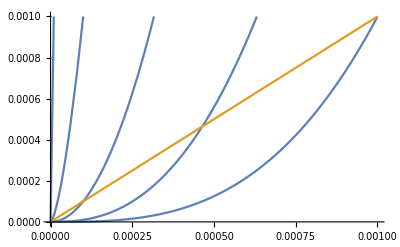

```mathematica
Plot[{Table[u^n/(.01^n+u^n),{n,{1,1.5,2,2.5,3}}],u},{u,0,.001},PlotRange->{0,.001}]
```

```mathematica
D[u^n/(K^n+u^n),u]/.u->0
```

-(0^(-1+2 n) n)/((0^n+K^n)^2)+(0^(-1+n) n)/(0^n+K^n)

```mathematica
Simplify[-(0^(-1+2 n) n)/((0^n+K^n)^2)+(0^(-1+n) n)/(0^n+K^n),Assumptions->n>0]
```

0^(-1+n) K^-n n

```mathematica
Root[{u^n/(K^n+u^n)-u,0}]
```

Root::nunipf: -u+u^n/(K^n+u^n) is not a univariate numeric pure function.

Root[{-u+u^n/(K^n+u^n),0}]

```mathematica
u1=K^(n/(n-1))+K^(2 n/(n-1))/(n-1)
```

K^(n/(-1+n))+K^((2 n)/(-1+n))/(-1+n)

```mathematica
Integrate[u^n/(K^n+u^n)-u,{u,0,u1},Assumptions->n>1&&K>0]
```

(K^((2 n)/(-1+n)) (-(-1+K^(n/(-1+n))+n)^2+(2 (-1+n)^(1-n) ((1/(-1+K^(n/(-1+n))+n))^n)^(-(1+n)/n) Hypergeometric2F1[1,1+1/n,2+1/n,-K^(n/(-1+n)) ((-1+n)/(-1+K^(n/(-1+n))+n))^-n])/(1+n)))/(2 (-1+n)^2)

```mathematica
Normal@Series[Sqrt[-2%],{K,0,1},Asssumptions->n>1&&K>0]
```

√(-1/(-1+n)^2 K^((2 n)/(-1+n)) (-(-1+K^(n/(-1+n))+n)^2+1/(1+n)2 (-1+n)^(1-n) ((1/(-1+K^(n/(-1+n))+n))^n)^(-(1+n)/n) (Hypergeometric2F1[1,1+1/n,2+1/n,-0^(n/(-1+n)) ((-1+n)/(-1+0^(n/(-1+n))+n))^-n]+1/(2+1/n)(1+1/n) (0^(n/(-1+n)) ((-1+n)/(-1+0^(n/(-1+n))+n))^-n-K^(n/(-1+n)) ((-1+n)/(-1+K^(n/(-1+n))+n))^-n) Hypergeometric2F1[2,2+1/n,3+1/n,-0^(n/(-1+n)) ((-1+n)/(-1+0^(n/(-1+n))+n))^-n]+1/(3+1/n)(1+1/n) (0^(n/(-1+n)) ((-1+n)/(-1+0^(n/(-1+n))+n))^-n-K^(n/(-1+n)) ((-1+n)/(-1+K^(n/(-1+n))+n))^-n)^2 Hypergeometric2F1[3,3+1/n,4+1/n,-0^(n/(-1+n)) ((-1+n)/(-1+0^(n/(-1+n))+n))^-n])))

```mathematica
FullSimplify[%,Assumptions->n>1&&K>0]
```

(K^(n/(-1+n)) √((-1+K^(n/(-1+n))+n)^2-(2 (-1+n)^(1-n) ((1/(-1+K^(n/(-1+n))+n))^n)^(-(1+n)/n) (1+K^(n/(-1+n)) (1+n) ((-1+n)/(-1+K^(n/(-1+n))+n))^(-2 n) (-(((-1+n)/(-1+K^(n/(-1+n))+n))^n)/(1+2 n)+K^(n/(-1+n))/(1+3 n))))/(1+n)))/(-1+n)

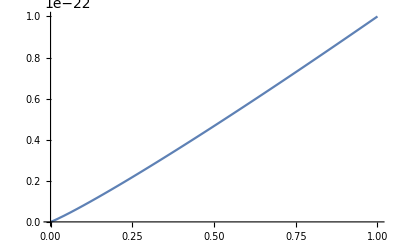

```mathematica
Plot[u^n/(K^n+u^n)/.{K->0.01,n->1.1},{u,0,u1/.{K->0.01,n->1.1}}]
```